```mathematica
Array[σ,4,0];
σ[0]=({{1, 0}, {0, 1}});
σ[1]=PauliMatrix[1];
σ[2]=PauliMatrix[2];
σ[3]=PauliMatrix[3];
σ[0,0]={{1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
u={{1},{0}};
d=({{0},{1}});
uu={1,0,0,0};
ud={0,1,0,0};
du={0,0,1,0};
dd={0,0,0,1};
p=Simplify[Cos[θ]u+ι Sin[θ]d];
m=Simplify[Cos[θ]u-ι Sin[θ]d];
ut=ConjugateTranspose[u];
dt=ConjugateTranspose[d];
pt=Simplify[ConjugateTranspose[p],0<θ<π];
mt=Simplify[ConjugateTranspose[m],0<θ<π];
MatrixForm[ut]
```

(1 | 0)

```mathematica
ψw=Simplify[c0(KroneckerProduct[u,u,d])+c1(KroneckerProduct[u,d,u])+(*√(1-c0^2-c1^2)*)c2(KroneckerProduct[d,u,u])];
ψwT=Simplify[ConjugateTranspose[ψw],{0<c1<1,0<(*√(1-c0^2-c1^2)*)c2<1,0<c0<1}];
ρw=Simplify[ψw.ψwT];
MatrixForm[ρw]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0^2 | c0 c1 | 0 | c0 c2 | 0 | 0 | 0
0 | c0 c1 | c1^2 | 0 | c1 c2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | c0 c2 | c1 c2 | 0 | c2^2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### W-state

#### Assemblages in 1SDI

```mathematica
For[l=1,l<4,l++,
For[i=0,i<2,i++,
Sw[i,l]=Simplify[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,σ[0],σ[0]].ρw.ConjugateTranspose[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,σ[0],σ[0]]]];
sw[i,l]=Simplify[ConjugateTranspose[KroneckerProduct[u,σ[0],σ[0]]].Sw[i,l].KroneckerProduct[u,σ[0],σ[0]]+ConjugateTranspose[KroneckerProduct[d,σ[0],σ[0]]].Sw[i,l].KroneckerProduct[d,σ[0],σ[0]]];
Print[Simplify[Tr[Sw[i,l]]]];
Print[{i,l-1}];
(*Print[MatrixForm[sw[i,l]]];*)
c0=1/(√3);c1=1/(√3);c2=1/(√3);
gw[i,l]=sw[i,l];
Print[MatrixForm[Simplify[gw[i,l]/Tr[gw[i,l]]]]];
Clear[c0,c1,c2];
Pgwf=Simplify[(1-((3 c0^2 c1^2)/c2^2))^(cp-1)];Pgws=Simplify[1-(1-((3 c0^2 c1^2)/c2^2))^(cp-1)];
gDw[i,l]=Simplify[Pgws*gw[i,l]+Pgwf*sw[i,l]];
]];
Clear[l,i,j,k]
```

1/2 (c0^2+c1^2+c2^2)

{0,0}

(1/3 | 1/3 | 1/3 | 0
1/3 | 1/3 | 1/3 | 0
1/3 | 1/3 | 1/3 | 0
0 | 0 | 0 | 0)

1/2 (c0^2+c1^2+c2^2)

{1,0}

(1/3 | -1/3 | -1/3 | 0
-1/3 | 1/3 | 1/3 | 0
-1/3 | 1/3 | 1/3 | 0
0 | 0 | 0 | 0)

1/2 (c0^2+c1^2+c2^2)

{0,1}

(1/3 | -ⅈ/3 | -ⅈ/3 | 0
ⅈ/3 | 1/3 | 1/3 | 0
ⅈ/3 | 1/3 | 1/3 | 0
0 | 0 | 0 | 0)

1/2 (c0^2+c1^2+c2^2)

{1,1}

(1/3 | ⅈ/3 | ⅈ/3 | 0
-ⅈ/3 | 1/3 | 1/3 | 0
-ⅈ/3 | 1/3 | 1/3 | 0
0 | 0 | 0 | 0)

c0^2+c1^2

{0,2}

(0 | 0 | 0 | 0
0 | 1/2 | 1/2 | 0
0 | 1/2 | 1/2 | 0
0 | 0 | 0 | 0)

c2^2

{1,2}

(1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
(*c0=1/√3;c1=1/√3;c2=√(1-c0^2-c1^2);*)
Simplify[Eigenvalues[({{0, 0, 0, 1/2}, {0, 1/2, 0, 0}, {0, 0, 1/2, 0}, {1/2, 0, 0, 0}})]]
Clear[c0,c1,c2]
```

{-1/2,1/2,1/2,1/2}

```mathematica
$Assumptions = {0<c1<1/(√3),1/(√3)<c2<2/(√3)};
(*c0 = √(1-c1^2-c2^2);*)
For[l=1,l<4,l++,
Fw[l]=Sum[√Tr[gw[i,l].gDw[i,l]],{i,0,1,1}]]
Simplify[1-(3 c0^2 c1^2)/c2^2]
FullSimplify[Fw[1]]
FullSimplify[Fw[2]]
FullSimplify[Fw[3]]
Clear[c0]
```

1-(3 c0^2 c1^2)/c2^2

(√(3+((1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (-3+(c0+c1+c2)^2))/(-3 c0^2 c1^2+c2^2)))/(√3)

(√(3+((1-(3 c0^2 c1^2)/c2^2)^cp c2^2 (-3+(c0+c1+c2)^2))/(-3 c0^2 c1^2+c2^2)))/(√3)

1/3 (√(1-(1-(3 c0^2 c1^2)/c2^2)^(-1+cp)+3 (1-(3 c0^2 c1^2)/c2^2)^(-1+cp) c2^2)+√(4-((-4+3 (c0+c1)^2) (1-(3 c0^2 c1^2)/c2^2)^cp c2^2)/(3 c0^2 c1^2-c2^2)))

```mathematica
Above assemblage fidelity expressions are simple and without replacing c0
```

```mathematica
$Assumptions = {0<c1<1/(√3),1/(√3)<c2<2/(√3)};
c0 = √(1-c1^2-c2^2);
For[l=1,l<4,l++,
Fw[l]=Sum[√Tr[gw[i,l].gDw[i,l]],{i,0,1,1}]]
Simplify[1-(3 c0^2 c1^2)/c2^2]
FullSimplify[Fw[1]]
FullSimplify[Fw[2]]
FullSimplify[Fw[3]]
Clear[c0]
```

(3 c1^4+c2^2+3 c1^2 (-1+c2^2))/c2^2

√((9 c1^4+3 c2^2+9 c1^2 (-1+c2^2)+2 c1 c2^2 (c2+√(1-c1^2-c2^2)) ((c2^2+3 c1^2 (-1+c1^2+c2^2))/c2^2)^cp+2 c2^2 (-1+c2 √(1-c1^2-c2^2)) ((c2^2+3 c1^2 (-1+c1^2+c2^2))/c2^2)^cp)/(3 c2^2+9 c1^2 (-1+c1^2+c2^2)))

√((9 c1^4+3 c2^2+9 c1^2 (-1+c2^2)+2 c1 c2^2 (c2+√(1-c1^2-c2^2)) ((c2^2+3 c1^2 (-1+c1^2+c2^2))/c2^2)^cp+2 c2^2 (-1+c2 √(1-c1^2-c2^2)) ((c2^2+3 c1^2 (-1+c1^2+c2^2))/c2^2)^cp)/(3 c2^2+9 c1^2 (-1+c1^2+c2^2)))

1/3 (√(1+c2^(2-2 cp) (-1+3 c2^2) (c2^2+3 c1^2 (-1+c1^2+c2^2))^(-1+cp))+√((4 c2^2+12 c1^2 (-1+c1^2+c2^2)+6 c1 c2^2 √(1-c1^2-c2^2) ((c2^2+3 c1^2 (-1+c1^2+c2^2))/c2^2)^cp-(c2^2+3 c2^4) ((c2^2+3 c1^2 (-1+c1^2+c2^2))/c2^2)^cp)/(c2^2+3 c1^2 (-1+c1^2+c2^2))))

```mathematica
Assemblages in 2SDI (*(Distillation not possible)*)
```

```mathematica
For[l=1,l<4,l++,
For[k=1,k<4,k++,
For[i=0,i<2,i++,
For[j=0,j<2,j++,
c2=c1;c1=√((1-c0^2)/2);
Sw[i,j,l,k]=Simplify[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,(σ[0]+(-1)^j σ[k])/2,σ[0]].ρw.ConjugateTranspose[KroneckerProduct[(σ[0]+(-1)^i σ[l])/2,(σ[0]+(-1)^j σ[k])/2,σ[0]]]];
(*Print[MatrixForm[Sw[i,j,k,l]]];*)
sw[i,j,l,k]=Simplify[ConjugateTranspose[KroneckerProduct[u,u,σ[0]]].Sw[i,j,l,k].KroneckerProduct[u,u,σ[0]]+ConjugateTranspose[KroneckerProduct[u,d,σ[0]]].Sw[i,j,l,k].KroneckerProduct[u,d,σ[0]]+ConjugateTranspose[KroneckerProduct[d,u,σ[0]]].Sw[i,j,l,k].KroneckerProduct[d,u,σ[0]]+ConjugateTranspose[KroneckerProduct[d,d,σ[0]]].Sw[i,j,l,k].KroneckerProduct[d,d,σ[0]]];
Print[{i,j,l-1,k-1}];
Print[MatrixForm[sw[i,j,l,k]]];
C0=({{c0/c1, 0}, {0, 1}});
(*c2=c1;*)
Print[MatrixForm[Simplify[C0.sw[i,j,l,k].C0]]];
Clear[C0];
c0=1/(√3);c1=1/(√3);c2=1/(√3);
gw[i,j,l,k]=sw[i,j,l,k];
Print[MatrixForm[gw[i,j,l,k]]];
Clear[c0,c1,c2];
Pgwf=Simplify[(1-(3 c0^2))^(cp-1)];Pgs=Simplify[1-(1-(3 c0^2))^(cp-1)];
gDw[i,j,l,k]=Simplify[Pgs*gw[i,j,l,k]+Pgwf*sw[i,j,l,k]];Print[MatrixForm[gDw[i,j,l,k]]]]]]]
Clear[l,i,j,k,c2,c1,c0,C0]
```

{0,0,0,0}

(1/2 (1-c0^2) | (c0 √(1-c0^2))/(2 √2)
(c0 √(1-c0^2))/(2 √2) | c0^2/4)

(c0^2 | c0^2/2
c0^2/2 | c0^2/4)

(1/3 | 1/6
1/6 | 1/12)

(1/6 (2+(1-3 c0^2)^cp) | 1/12 (2-2 (1-3 c0^2)^(-1+cp)+3 c0 (1-3 c0^2)^(-1+cp) √(2-2 c0^2))
1/12 (2-2 (1-3 c0^2)^(-1+cp)+3 c0 (1-3 c0^2)^(-1+cp) √(2-2 c0^2)) | 1/12 (1-(1-3 c0^2)^cp))

{0,1,0,0}

(0 | 0
0 | c0^2/4)

(0 | 0
0 | c0^2/4)

(0 | 0
0 | 1/12)

(0 | 0
0 | 1/12 (1-(1-3 c0^2)^cp))

{1,0,0,0}

(0 | 0
0 | c0^2/4)

(0 | 0
0 | c0^2/4)

(0 | 0
0 | 1/12)

(0 | 0
0 | 1/12 (1-(1-3 c0^2)^cp))

{1,1,0,0}

(1/2 (1-c0^2) | -(c0 √(1-c0^2))/(2 √2)
-(c0 √(1-c0^2))/(2 √2) | c0^2/4)

(c0^2 | -c0^2/2
-c0^2/2 | c0^2/4)

(1/3 | -1/6
-1/6 | 1/12)

(1/6 (2+(1-3 c0^2)^cp) | -(c0 (1-3 c0^2)^(-1+cp) √(1-c0^2))/(2 √2)+1/6 (-1+(1-3 c0^2)^(-1+cp))
-(c0 (1-3 c0^2)^(-1+cp) √(1-c0^2))/(2 √2)+1/6 (-1+(1-3 c0^2)^(-1+cp)) | 1/12 (1-(1-3 c0^2)^cp))

{0,0,0,1}

(1/4 (1-c0^2) | ((1/4-ⅈ/4) c0 √(1-c0^2))/(√2)
((1/4+ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

(c0^2/2 | (1/4-ⅈ/4) c0^2
(1/4+ⅈ/4) c0^2 | c0^2/4)

(1/6 | 1/12-ⅈ/12
1/12+ⅈ/12 | 1/12)

(1/12 (2+(1-3 c0^2)^cp) | -((1-ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2)
-((1+ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2) | 1/12 (1-(1-3 c0^2)^cp))

{0,1,0,1}

(1/4 (1-c0^2) | ((1/4+ⅈ/4) c0 √(1-c0^2))/(√2)
((1/4-ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

(c0^2/2 | (1/4+ⅈ/4) c0^2
(1/4-ⅈ/4) c0^2 | c0^2/4)

(1/6 | 1/12+ⅈ/12
1/12-ⅈ/12 | 1/12)

(1/12 (2+(1-3 c0^2)^cp) | -((1+ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2)
-((1-ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2) | 1/12 (1-(1-3 c0^2)^cp))

{1,0,0,1}

(1/4 (1-c0^2) | -((1/4+ⅈ/4) c0 √(1-c0^2))/(√2)
-((1/4-ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

(c0^2/2 | (-1/4-ⅈ/4) c0^2
(-1/4+ⅈ/4) c0^2 | c0^2/4)

(1/6 | -1/12-ⅈ/12
-1/12+ⅈ/12 | 1/12)

(1/12 (2+(1-3 c0^2)^cp) | ((1+ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2)
((1-ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2) | 1/12 (1-(1-3 c0^2)^cp))

{1,1,0,1}

(1/4 (1-c0^2) | -((1/4-ⅈ/4) c0 √(1-c0^2))/(√2)
-((1/4+ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

(c0^2/2 | (-1/4+ⅈ/4) c0^2
(-1/4-ⅈ/4) c0^2 | c0^2/4)

(1/6 | -1/12+ⅈ/12
-1/12-ⅈ/12 | 1/12)

(1/12 (2+(1-3 c0^2)^cp) | ((1-ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2)
((1+ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2) | 1/12 (1-(1-3 c0^2)^cp))

{0,0,0,2}

(1/4 (1-c0^2) | (c0 √(1-c0^2))/(2 √2)
(c0 √(1-c0^2))/(2 √2) | c0^2/2)

(c0^2/2 | c0^2/2
c0^2/2 | c0^2/2)

(1/6 | 1/6
1/6 | 1/6)

(1/12 (2+(1-3 c0^2)^cp) | 1/12 (2-2 (1-3 c0^2)^(-1+cp)+3 c0 (1-3 c0^2)^(-1+cp) √(2-2 c0^2))
1/12 (2-2 (1-3 c0^2)^(-1+cp)+3 c0 (1-3 c0^2)^(-1+cp) √(2-2 c0^2)) | 1/6 (1-(1-3 c0^2)^cp))

{0,1,0,2}

(1/4 (1-c0^2) | 0
0 | 0)

(c0^2/2 | 0
0 | 0)

(1/6 | 0
0 | 0)

(1/12 (2+(1-3 c0^2)^cp) | 0
0 | 0)

{1,0,0,2}

(1/4 (1-c0^2) | -(c0 √(1-c0^2))/(2 √2)
-(c0 √(1-c0^2))/(2 √2) | c0^2/2)

(c0^2/2 | -c0^2/2
-c0^2/2 | c0^2/2)

(1/6 | -1/6
-1/6 | 1/6)

(1/12 (2+(1-3 c0^2)^cp) | -(c0 (1-3 c0^2)^(-1+cp) √(1-c0^2))/(2 √2)+1/6 (-1+(1-3 c0^2)^(-1+cp))
-(c0 (1-3 c0^2)^(-1+cp) √(1-c0^2))/(2 √2)+1/6 (-1+(1-3 c0^2)^(-1+cp)) | 1/6 (1-(1-3 c0^2)^cp))

{1,1,0,2}

(1/4 (1-c0^2) | 0
0 | 0)

(c0^2/2 | 0
0 | 0)

(1/6 | 0
0 | 0)

(1/12 (2+(1-3 c0^2)^cp) | 0
0 | 0)

{0,0,1,0}

(1/4 (1-c0^2) | ((1/4-ⅈ/4) c0 √(1-c0^2))/(√2)
((1/4+ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

(c0^2/2 | (1/4-ⅈ/4) c0^2
(1/4+ⅈ/4) c0^2 | c0^2/4)

(1/6 | 1/12-ⅈ/12
1/12+ⅈ/12 | 1/12)

(1/12 (2+(1-3 c0^2)^cp) | -((1-ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2)
-((1+ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2) | 1/12 (1-(1-3 c0^2)^cp))

{0,1,1,0}

(1/4 (1-c0^2) | -((1/4+ⅈ/4) c0 √(1-c0^2))/(√2)
-((1/4-ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

(c0^2/2 | (-1/4-ⅈ/4) c0^2
(-1/4+ⅈ/4) c0^2 | c0^2/4)

(1/6 | -1/12-ⅈ/12
-1/12+ⅈ/12 | 1/12)

(1/12 (2+(1-3 c0^2)^cp) | ((1+ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2)
((1-ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2) | 1/12 (1-(1-3 c0^2)^cp))

{1,0,1,0}

(1/4 (1-c0^2) | ((1/4+ⅈ/4) c0 √(1-c0^2))/(√2)
((1/4-ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

(c0^2/2 | (1/4+ⅈ/4) c0^2
(1/4-ⅈ/4) c0^2 | c0^2/4)

(1/6 | 1/12+ⅈ/12
1/12-ⅈ/12 | 1/12)

(1/12 (2+(1-3 c0^2)^cp) | -((1+ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2)
-((1-ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2) | 1/12 (1-(1-3 c0^2)^cp))

{1,1,1,0}

(1/4 (1-c0^2) | -((1/4-ⅈ/4) c0 √(1-c0^2))/(√2)
-((1/4+ⅈ/4) c0 √(1-c0^2))/(√2) | c0^2/4)

(c0^2/2 | (-1/4+ⅈ/4) c0^2
(-1/4-ⅈ/4) c0^2 | c0^2/4)

(1/6 | -1/12+ⅈ/12
-1/12-ⅈ/12 | 1/12)

(1/12 (2+(1-3 c0^2)^cp) | ((1-ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2)
((1+ⅈ) (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-24+72 c0^2) | 1/12 (1-(1-3 c0^2)^cp))

{0,0,1,1}

(1/2 (1-c0^2) | -(ⅈ c0 √(1-c0^2))/(2 √2)
(ⅈ c0 √(1-c0^2))/(2 √2) | c0^2/4)

(c0^2 | -(ⅈ c0^2)/2
(ⅈ c0^2)/2 | c0^2/4)

(1/3 | -ⅈ/6
ⅈ/6 | 1/12)

(1/6 (2+(1-3 c0^2)^cp) | (ⅈ (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-12+36 c0^2)
1/12 ⅈ (2-2 (1-3 c0^2)^(-1+cp)+3 c0 (1-3 c0^2)^(-1+cp) √(2-2 c0^2)) | 1/12 (1-(1-3 c0^2)^cp))

{0,1,1,1}

(0 | 0
0 | c0^2/4)

(0 | 0
0 | c0^2/4)

(0 | 0
0 | 1/12)

(0 | 0
0 | 1/12 (1-(1-3 c0^2)^cp))

{1,0,1,1}

(0 | 0
0 | c0^2/4)

(0 | 0
0 | c0^2/4)

(0 | 0
0 | 1/12)

(0 | 0
0 | 1/12 (1-(1-3 c0^2)^cp))

{1,1,1,1}

(1/2 (1-c0^2) | (ⅈ c0 √(1-c0^2))/(2 √2)
-(ⅈ c0 √(1-c0^2))/(2 √2) | c0^2/4)

(c0^2 | (ⅈ c0^2)/2
-(ⅈ c0^2)/2 | c0^2/4)

(1/3 | ⅈ/6
-ⅈ/6 | 1/12)

(1/6 (2+(1-3 c0^2)^cp) | 1/12 ⅈ (2-2 (1-3 c0^2)^(-1+cp)+3 c0 (1-3 c0^2)^(-1+cp) √(2-2 c0^2))
(ⅈ (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-12+36 c0^2) | 1/12 (1-(1-3 c0^2)^cp))

{0,0,1,2}

(1/4 (1-c0^2) | -(ⅈ c0 √(1-c0^2))/(2 √2)
(ⅈ c0 √(1-c0^2))/(2 √2) | c0^2/2)

(c0^2/2 | -(ⅈ c0^2)/2
(ⅈ c0^2)/2 | c0^2/2)

(1/6 | -ⅈ/6
ⅈ/6 | 1/6)

(1/12 (2+(1-3 c0^2)^cp) | (ⅈ (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-12+36 c0^2)
1/12 ⅈ (2-2 (1-3 c0^2)^(-1+cp)+3 c0 (1-3 c0^2)^(-1+cp) √(2-2 c0^2)) | 1/6 (1-(1-3 c0^2)^cp))

{0,1,1,2}

(1/4 (1-c0^2) | 0
0 | 0)

(c0^2/2 | 0
0 | 0)

(1/6 | 0
0 | 0)

(1/12 (2+(1-3 c0^2)^cp) | 0
0 | 0)

{1,0,1,2}

(1/4 (1-c0^2) | (ⅈ c0 √(1-c0^2))/(2 √2)
-(ⅈ c0 √(1-c0^2))/(2 √2) | c0^2/2)

(c0^2/2 | (ⅈ c0^2)/2
-(ⅈ c0^2)/2 | c0^2/2)

(1/6 | ⅈ/6
-ⅈ/6 | 1/6)

(1/12 (2+(1-3 c0^2)^cp) | 1/12 ⅈ (2-2 (1-3 c0^2)^(-1+cp)+3 c0 (1-3 c0^2)^(-1+cp) √(2-2 c0^2))
(ⅈ (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-12+36 c0^2) | 1/6 (1-(1-3 c0^2)^cp))

{1,1,1,2}

(1/4 (1-c0^2) | 0
0 | 0)

(c0^2/2 | 0
0 | 0)

(1/6 | 0
0 | 0)

(1/12 (2+(1-3 c0^2)^cp) | 0
0 | 0)

{0,0,2,0}

(1/4 (1-c0^2) | (c0 √(1-c0^2))/(2 √2)
(c0 √(1-c0^2))/(2 √2) | c0^2/2)

(c0^2/2 | c0^2/2
c0^2/2 | c0^2/2)

(1/6 | 1/6
1/6 | 1/6)

(1/12 (2+(1-3 c0^2)^cp) | 1/12 (2-2 (1-3 c0^2)^(-1+cp)+3 c0 (1-3 c0^2)^(-1+cp) √(2-2 c0^2))
1/12 (2-2 (1-3 c0^2)^(-1+cp)+3 c0 (1-3 c0^2)^(-1+cp) √(2-2 c0^2)) | 1/6 (1-(1-3 c0^2)^cp))

{0,1,2,0}

(1/4 (1-c0^2) | -(c0 √(1-c0^2))/(2 √2)
-(c0 √(1-c0^2))/(2 √2) | c0^2/2)

(c0^2/2 | -c0^2/2
-c0^2/2 | c0^2/2)

(1/6 | -1/6
-1/6 | 1/6)

(1/12 (2+(1-3 c0^2)^cp) | -(c0 (1-3 c0^2)^(-1+cp) √(1-c0^2))/(2 √2)+1/6 (-1+(1-3 c0^2)^(-1+cp))
-(c0 (1-3 c0^2)^(-1+cp) √(1-c0^2))/(2 √2)+1/6 (-1+(1-3 c0^2)^(-1+cp)) | 1/6 (1-(1-3 c0^2)^cp))

{1,0,2,0}

(1/4 (1-c0^2) | 0
0 | 0)

(c0^2/2 | 0
0 | 0)

(1/6 | 0
0 | 0)

(1/12 (2+(1-3 c0^2)^cp) | 0
0 | 0)

{1,1,2,0}

(1/4 (1-c0^2) | 0
0 | 0)

(c0^2/2 | 0
0 | 0)

(1/6 | 0
0 | 0)

(1/12 (2+(1-3 c0^2)^cp) | 0
0 | 0)

{0,0,2,1}

(1/4 (1-c0^2) | -(ⅈ c0 √(1-c0^2))/(2 √2)
(ⅈ c0 √(1-c0^2))/(2 √2) | c0^2/2)

(c0^2/2 | -(ⅈ c0^2)/2
(ⅈ c0^2)/2 | c0^2/2)

(1/6 | -ⅈ/6
ⅈ/6 | 1/6)

(1/12 (2+(1-3 c0^2)^cp) | (ⅈ (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-12+36 c0^2)
1/12 ⅈ (2-2 (1-3 c0^2)^(-1+cp)+3 c0 (1-3 c0^2)^(-1+cp) √(2-2 c0^2)) | 1/6 (1-(1-3 c0^2)^cp))

{0,1,2,1}

(1/4 (1-c0^2) | (ⅈ c0 √(1-c0^2))/(2 √2)
-(ⅈ c0 √(1-c0^2))/(2 √2) | c0^2/2)

(c0^2/2 | (ⅈ c0^2)/2
-(ⅈ c0^2)/2 | c0^2/2)

(1/6 | ⅈ/6
-ⅈ/6 | 1/6)

(1/12 (2+(1-3 c0^2)^cp) | 1/12 ⅈ (2-2 (1-3 c0^2)^(-1+cp)+3 c0 (1-3 c0^2)^(-1+cp) √(2-2 c0^2))
(ⅈ (2-6 c0^2-2 (1-3 c0^2)^cp+3 c0 (1-3 c0^2)^cp √(2-2 c0^2)))/(-12+36 c0^2) | 1/6 (1-(1-3 c0^2)^cp))

{1,0,2,1}

(1/4 (1-c0^2) | 0
0 | 0)

(c0^2/2 | 0
0 | 0)

(1/6 | 0
0 | 0)

(1/12 (2+(1-3 c0^2)^cp) | 0
0 | 0)

{1,1,2,1}

(1/4 (1-c0^2) | 0
0 | 0)

(c0^2/2 | 0
0 | 0)

(1/6 | 0
0 | 0)

(1/12 (2+(1-3 c0^2)^cp) | 0
0 | 0)

{0,0,2,2}

(0 | 0
0 | c0^2)

(0 | 0
0 | c0^2)

(0 | 0
0 | 1/3)

(0 | 0
0 | 1/3 (1-(1-3 c0^2)^cp))

{0,1,2,2}

(1/2 (1-c0^2) | 0
0 | 0)

(c0^2 | 0
0 | 0)

(1/3 | 0
0 | 0)

(1/6 (2+(1-3 c0^2)^cp) | 0
0 | 0)

{1,0,2,2}

(1/2 (1-c0^2) | 0
0 | 0)

(c0^2 | 0
0 | 0)

(1/3 | 0
0 | 0)

(1/6 (2+(1-3 c0^2)^cp) | 0
0 | 0)

{1,1,2,2}

(0 | 0
0 | 0)

(0 | 0
0 | 0)

(0 | 0
0 | 0)

«1 more identical outputs»

```mathematica
(*c0= (√2)/(√3(√(1+γ-λ)));c1=(√2)/(√3(√(1+γ+λ)));c2=(√2)/(√3(√(1+γ+λ)));*)
MatrixForm[Simplify[sw[1,0,2,2]]]
Simplify[Tr[Sw[1,0,2,2]]]
(*MatrixForm[gw[0,0,1,1]]
Simplify[Tr[gw[0,0,1,1]]]*)
Clear[c0,c1,c2]
```

```mathematica
b=Simplify[(c1- c2)u+I c0 d];
bT=Simplify[ConjugateTranspose[b],{0<c0<1,0<c2<1,0<c1<1}];
MatrixForm[Simplify[b.bT]]
```

```mathematica
Probability of getting outcome 0 in 2SDI w-state
```

```mathematica
c1=√((1-c0^2)/2);
C0=({{c0/c1, 0}, {0, 1}});
P12SW=Simplify[Tr[C0.(sw[0,0,1,1]+sw[0,1,1,1]+sw[1,0,1,1]+sw[1,1,1,1]).C0]];
P22sW=Simplify[Tr[C0.(sw[0,0,2,1]+sw[0,1,2,1]+sw[1,0,2,1]+sw[1,1,2,1]).C0]];
P32SW=Simplify[Tr[C0.(sw[0,0,3,1]+sw[0,1,3,1]+sw[1,0,3,1]+sw[1,1,3,1]).C0]];
P42sW=Simplify[Tr[C0.(sw[0,0,1,2]+sw[0,1,1,2]+sw[1,0,1,2]+sw[1,1,1,2]).C0]];
P52SW=Simplify[Tr[C0.(sw[0,0,1,3]+sw[0,1,1,3]+sw[1,0,1,3]+sw[1,1,1,3]).C0]];
P62SW=Simplify[Tr[C0.(sw[0,0,2,2]+sw[0,1,2,2]+sw[1,0,2,2]+sw[1,1,2,2]).C0]];
P72SW=Simplify[Tr[C0.(sw[0,0,3,2]+sw[0,1,3,2]+sw[1,0,3,2]+sw[1,1,3,2]).C0]];
P82SW=Simplify[Tr[C0.(sw[0,0,2,3]+sw[0,1,2,3]+sw[1,0,2,3]+sw[1,1,2,3]).C0]];
P92SW=Simplify[Tr[C0.(sw[0,0,3,3]+sw[0,1,3,3]+sw[1,0,3,3]+sw[1,1,3,3]).C0]];
For[l=1,l<4,l++,
For[k=1,k<4,k++,
For[i=0,i<2,i++,
For[j=0,j<2,j++,
P2SW[l,k]=Simplify[Sum[Tr[C0.sw[i,j,l,k].C0],{i,0,1,1},{j,0,1,1}]]]]Print[{l-1,k-1}];Print[P2SW[l,k]]]]
Clear[C0,c1]
```

{0,0}

3 c0^2

{0,1}

3 c0^2

{0,2}

3 c0^2

{1,0}

3 c0^2

{1,1}

3 c0^2

{1,2}

3 c0^2

{2,0}

3 c0^2

{2,1}

3 c0^2

{2,2}

3 c0^2

```mathematica
Assemblage fidelity of w-state in 2SDI
```

```mathematica
Fw2S00=Simplify[√Tr[gw[0,0,1,1].gDw[0,0,1,1]]+√Tr[gw[0,1,1,1].gDw[0,1,1,1]]+√Tr[gw[1,0,1,1].gDw[1,0,1,1]]+√Tr[gw[1,1,1,1].gDw[1,1,1,1]]]
```

1/6 (√(1-(1-3 c0^2)^cp)+√((-25+(1-3 c0^2)^cp-12 c0 (1-3 c0^2)^cp √(2-2 c0^2)+3 c0^2 (25+7 (1-3 c0^2)^cp))/(-1+3 c0^2)))

```mathematica
For[l=1,l<4,l++,
For[k=1,k<4,k++,
F2Sw[l,k]=FullSimplify[Sum[√Tr[gw[i,j,l,k].gDw[i,j,l,k]],{i,0,1,1},{j,0,1,1}]];Print[{l-1,k-1}];Print[F2Sw[l,k]]]]
```

{0,0}

1/6 (√(1-(1-3 c0^2)^cp)+√((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2)))

{0,1}

√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2))

{0,2}

(√(2+(1-3 c0^2)^cp)+√((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2)))/(3 √2)

{1,0}

√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2))

{1,1}

1/6 (√(1-(1-3 c0^2)^cp)+√((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2)))

{1,2}

(√(2+(1-3 c0^2)^cp)+√((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2)))/(3 √2)

{2,0}

(√(2+(1-3 c0^2)^cp)+√((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2)))/(3 √2)

{2,1}

(√(2+(1-3 c0^2)^cp)+√((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2)))/(3 √2)

{2,2}

1/3 (√(1-(1-3 c0^2)^cp)+√2 √(2+(1-3 c0^2)^cp))

```mathematica
c0=0.4;cp=2;
Simplify[F2Sw[1,1]]
Simplify[F2Sw[1,2]]
Simplify[F2Sw[1,3]]
Simplify[F2Sw[2,1]]
Simplify[F2Sw[2,2]]
Simplify[F2Sw[2,3]]
Simplify[F2Sw[3,1]]
Simplify[F2Sw[3,2]]
Simplify[F2Sw[3,3]]
Clear[c0,cp]
```

0.991674

0.989275

0.990552

0.989275

0.991674

0.990552

0.990552

0.990552

0.995027

```mathematica
F2Sw[0,1] is minimum and it is shown as F0
```

```mathematica
Simplify[Expand[(√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2)))^2-(1/9+1/18 (1-3 c0^2)^cp-4/(9 (-1+3 c0^2))+(4 c0^2)/(3 (-1+3 c0^2))+(5 (1-3 c0^2)^cp)/(18 (-1+3 c0^2))-(c0^2 (1-3 c0^2)^cp)/(6 (-1+3 c0^2))-(c0 (1-3 c0^2)^cp √(2-2 c0^2))/(3 (-1+3 c0^2)))]]
```

(-4+(1-3 c0^2)^cp-3 c0 (1-3 c0^2)^cp √(2-2 c0^2)+3 c0^2 (4+(1-3 c0^2)^cp))/(-9+27 c0^2)

```mathematica
(4-Y^N+3 c0 Y^N √(2-2 c0^2)-3 c0^2 (4+Y^N))/(9Y)
```

```mathematica
Simplify[Expand[((-4+(1-3 c0^2)^cp-3 c0 (1-3 c0^2)^cp √(2-2 c0^2)+3 c0^2 (4+(1-3 c0^2)^cp))/(-9+27 c0^2))^2]]
```

1/(81 (1-3 c0^2)^2)(-6 c0 (1-3 c0^2)^cp √(2-2 c0^2) (-4+(1-3 c0^2)^cp)+(-4+(1-3 c0^2)^cp)^2-18 c0^3 (1-3 c0^2)^cp √(2-2 c0^2) (4+(1-3 c0^2)^cp)+24 c0^2 (-4+(1-3 c0^2)^(2 cp))-9 c0^4 (-16-8 (1-3 c0^2)^cp+(1-3 c0^2)^(2 cp)))

```mathematica
F(0,2) assemblage fidelity shown as F3
```

```mathematica
1/9+1/18 Y^N+4/(9 Y)-(4 c0^2)/(3 Y)-(5 Y^(N-1))/18+(c0^2 Y^(N-1))/6+(c0 Y^(N-1) √(2-2 c0^2))/3
```

```mathematica
Expand[(1/(3 √2)(√(2+(1-3 c0^2)^cp)+√((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2))))^2-(1/9+1/18 (1-3 c0^2)^cp-4/(9 (-1+3 c0^2))+(4 c0^2)/(3 (-1+3 c0^2))+(5 (1-3 c0^2)^cp)/(18 (-1+3 c0^2))-(c0^2 (1-3 c0^2)^cp)/(6 (-1+3 c0^2))-(c0 (1-3 c0^2)^cp √(2-2 c0^2))/(3 (-1+3 c0^2)))]
```

1/9 √(2+(1-3 c0^2)^cp) √((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2))

```mathematica
1/9 √(2+Y^N) √((8-5 Y^N+3 c0 (2 Y^N √(2-2 c0^2)+c0 (-8+Y^N)))/Y)
```

```mathematica
Simplify[Expand[(1/9 √(2+(1-3 c0^2)^cp) √((-8+5 (1-3 c0^2)^cp-3 c0 (2 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (-8+(1-3 c0^2)^cp)))/(-1+3 c0^2)))^2]]
```

-(((2+(1-3 c0^2)^cp) (8-5 (1-3 c0^2)^cp+6 c0 (1-3 c0^2)^cp √(2-2 c0^2)+3 c0^2 (-8+(1-3 c0^2)^cp)))/(81 (-1+3 c0^2)))

```mathematica
Difference between (F0^2-A)^2-(F2^2-A)^2
```

```mathematica
FullSimplify[1/(81 (1-3 c0^2)^2)(-6 c0 (1-3 c0^2)^cp √(2-2 c0^2) (-4+(1-3 c0^2)^cp)+(-4+(1-3 c0^2)^cp)^2-18 c0^3 (1-3 c0^2)^cp √(2-2 c0^2) (4+(1-3 c0^2)^cp)+24 c0^2 (-4+(1-3 c0^2)^(2 cp))-9 c0^4 (-16-8 (1-3 c0^2)^cp+(1-3 c0^2)^(2 cp)))-(-(((2+(1-3 c0^2)^cp) (8-5 (1-3 c0^2)^cp+6 c0 (1-3 c0^2)^cp √(2-2 c0^2)+3 c0^2 (-8+(1-3 c0^2)^cp)))/(81 (-1+3 c0^2))))]
```

-2/27 (1-3 c0^2)^(-2+cp) (-1+3 c0^2+(1-3 c0^2)^cp) (-1-c0^2+2 c0 √(2-2 c0^2))

```mathematica
-2/27 Y^(N-1) (Y^(N-1)-1) (-1-c0^2+2 c0 √(2-2 c0^2))
```

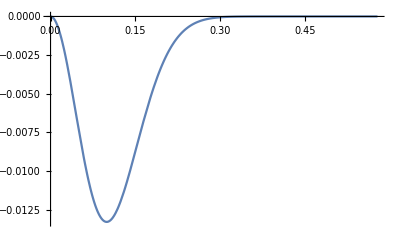

```mathematica
cp=20;
Plot[-2/27 (1-3 c0^2)^(-2+cp) (-1+3 c0^2+(1-3 c0^2)^cp) (-1-c0^2+2 c0 √(2-2 c0^2)),{c0,0,1/√3}]
Clear[cp]
```

```mathematica
F(0,0) is shown as F2
```

```mathematica
Expand[(1/6 (√(1-(1-3 c0^2)^cp)+√((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2))))^2]
```

1/36-1/36 (1-3 c0^2)^cp-25/(36 (-1+3 c0^2))+(25 c0^2)/(12 (-1+3 c0^2))+((1-3 c0^2)^cp)/(36 (-1+3 c0^2))+(7 c0^2 (1-3 c0^2)^cp)/(12 (-1+3 c0^2))-(c0 (1-3 c0^2)^cp √(2-2 c0^2))/(3 (-1+3 c0^2))+1/18 √(1-(1-3 c0^2)^cp) √((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2))

```mathematica
1/18 √(1-Y^N) √((25-Y^N-3 c0 (-4 Y^N √(2-2 c0^2)+c0 (25+7 Y^N)))/Y)
```

```mathematica
Simplify[Expand[(1/6 (√(1-(1-3 c0^2)^cp)+√((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2))))^2-(1/36-1/36 (1-3 c0^2)^cp-25/(36 (-1+3 c0^2))+(25 c0^2)/(12 (-1+3 c0^2))+((1-3 c0^2)^cp)/(36 (-1+3 c0^2))+(7 c0^2 (1-3 c0^2)^cp)/(12 (-1+3 c0^2))-(c0 (1-3 c0^2)^cp √(2-2 c0^2))/(3 (-1+3 c0^2)))]]
```

1/18 √(1-(1-3 c0^2)^cp) √((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2))

```mathematica
Simplify[Expand[(√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2)))^2-(1/36-1/36 (1-3 c0^2)^cp-25/(36 (-1+3 c0^2))+(25 c0^2)/(12 (-1+3 c0^2))+((1-3 c0^2)^cp)/(36 (-1+3 c0^2))+(7 c0^2 (1-3 c0^2)^cp)/(12 (-1+3 c0^2))-(c0 (1-3 c0^2)^cp √(2-2 c0^2))/(3 (-1+3 c0^2)))]]
```

(-6 c0 (1-3 c0^2)^cp √(2-2 c0^2)-3 c0^2 (-5+(1-3 c0^2)^cp)+5 (-1+(1-3 c0^2)^cp))/(-18+54 c0^2)

```mathematica
(6 c0 Y^N √(2-2 c0^2)-3 c0^2 (5-Y^N)+5 (1-Y^N))/(18Y)
```

```mathematica
Simplify[Expand[((-6 c0 (1-3 c0^2)^cp √(2-2 c0^2)-3 c0^2 (-5+(1-3 c0^2)^cp)+5 (-1+(1-3 c0^2)^cp))/(-18+54 c0^2))^2-(1/18 √(1-(1-3 c0^2)^cp) √((-25+(1-3 c0^2)^cp+3 c0 (-4 (1-3 c0^2)^cp √(2-2 c0^2)+c0 (25+7 (1-3 c0^2)^cp)))/(-1+3 c0^2)))^2]]
```

-2/27 (1-3 c0^2)^(-2+cp) (-1+3 c0^2+(1-3 c0^2)^cp) (-1-c0^2+2 c0 √(2-2 c0^2))

```mathematica
-2/27 Y^(N-1) (Y^(N-1)-1) (-1-c0^2+2 c0 √(2-2 c0^2))
```

```mathematica
F(2,2)
```

```mathematica
Expand[(1/3 (√(1-(1-3 c0^2)^cp)+√2 √(2+(1-3 c0^2)^cp)))^2]
```

5/9+1/9 (1-3 c0^2)^cp+2/9 √2 √(1-(1-3 c0^2)^cp) √(2+(1-3 c0^2)^cp)

```mathematica
Simplify[Expand[(1/3 (√(1-(1-3 c0^2)^cp)+√2 √(2+(1-3 c0^2)^cp)))^2-(5/9+1/9 (1-3 c0^2)^cp)]]
```

2/9 √2 √(-(-1+(1-3 c0^2)^cp) (2+(1-3 c0^2)^cp))

```mathematica
2/9 √2 √((1-Y^N) (2+Y^N))
```

```mathematica
(5/9+1/9 Y^N)
```

```mathematica
Simplify[Expand[(√((-3+(1-3 c0^2)^cp-2 c0 (1-3 c0^2)^cp √(2-2 c0^2)+c0^2 (9+(1-3 c0^2)^cp))/(-3+9 c0^2)))^2-(5/9+1/9 (1-3 c0^2)^cp)]]
```

(-4+12 c0^2+4 (1-3 c0^2)^cp-6 c0 (1-3 c0^2)^cp √(2-2 c0^2))/(-9+27 c0^2)

```mathematica
(4-12 c0^2-4 Y^N+6 c0 Y^N √(2-2 c0^2))/(9Y)
```

```mathematica
Simplify[Expand[((-4+12 c0^2+4 (1-3 c0^2)^cp-6 c0 (1-3 c0^2)^cp √(2-2 c0^2))/(-9+27 c0^2))^2-(2/9 √2 √(-(-1+(1-3 c0^2)^cp) (2+(1-3 c0^2)^cp)))^2]]
```

-8/27 (1-3 c0^2)^(-2+cp) (-1+3 c0^2+(1-3 c0^2)^cp) (-1-c0^2+2 c0 √(2-2 c0^2))